```mathematica
ClearAll["Global`*"];
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
rplus = M+Sqrt[M^2-a^2];
tt=2 M r/ρ-1;
rr=ρ/Δ;
θθ=ρ;
ϕϕ=(Δ+(2 M r (r^2+a^2))/ρ)Sin[θ]^2;
tϕ=-4 a M r Sin[θ]^2/ρ;
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
```

```mathematica
a=0;M=.;
ρ=r^2+a^2 Cos[θ]^2;
Δ=r^2 - 2 M r+ a^2;
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ]
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}]]
```

```mathematica
TableForm[Partition[DeleteCases[Flatten[listchristoffel],Null],2],TableSpacing->{2,2}]
TableForm[Partition[DeleteCases[Flatten[listgeodesic],Null],2],TableSpacing->{2,2}]
```

Γ[1, 2, 1] | -M/(2 M r-r^2)
Γ[2, 1, 1] | (M (-2 M+r))/r^3
Γ[2, 2, 2] | M/(2 M r-r^2)
Γ[2, 3, 3] | 2 M-r
Γ[2, 4, 4] | (2 M-r) Sin[θ]^2
Γ[3, 3, 2] | 1/r
Γ[3, 4, 4] | -Cos[θ] Sin[θ]
Γ[4, 4, 2] | 1/r
Γ[4, 4, 3] | Cot[θ]

d/dτ t' | =
(2 M r' t')/(2 M r-r^2) | d/dτ r'
= | (-M r^2 (r')^2+(-2 M+r)^2 (M (t')^2-r^3 ((θ')^2+Sin[θ]^2 (ϕ')^2)))/((2 M-r) r^3)
d/dτ θ' | =
-(2 r' θ')/r+Cos[θ] Sin[θ] (ϕ')^2 | d/dτ ϕ'
= | -(2 (r'+r Cot[θ] θ') ϕ')/r

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>Re[coords[[2]][τ]]≤2,"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=r[τ] Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=r[τ] Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=r[τ] Cos[θ[τ]]/.soln;{xs,ys,zs}]
```

```mathematica
uinvar=0;M=1; τval=20; rplus = M + Sqrt[M^2-a^2];
ivs = {-0.15,0.0,0.001}; ics = {0,5,π/3,π/4};
solution = computeSoln[τval,ivs,ics];
τend
```

NDSolve::evre: The value of the event function at τ = 0.000402524 was not a real number. The event will be ignored in steps where it does not evaluate to real numbers at both ends.

τend

2.88699

4.99994

1.04724

0.799683

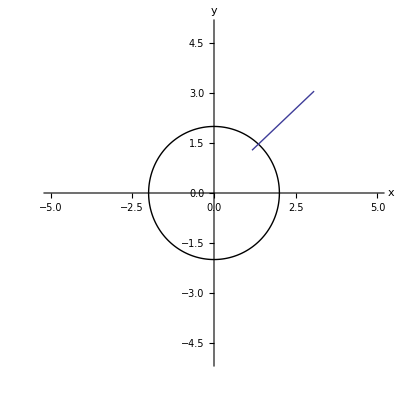

```mathematica
it = solution[[1]][[1]][[2]]; it[τval/2]
ir = solution[[1]][[2]][[2]]; ir[0.0004025237467436282]
iθ = solution[[1]][[3]][[2]]; iθ[τval/2]
iϕ = solution[[1]][[4]][[2]]; iϕ[τval/2]
xyz=sphslnToCartsln[solution];
horizpl=PolarPlot[rplus,{θ,0,2 Pi},DisplayFunction->Identity,PlotStyle->{Black,Thick}];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τval},DisplayFunction->Identity];
Show[horizpl,%,DisplayFunction->$DisplayFunction,AxesLabel->{x,y},PlotRange -> {{-5,5},{-5,5}}]
```